```mathematica
Expand[(x+y)^5*(x+y+z)^2]
```

x^7+7 x^6 y+21 x^5 y^2+35 x^4 y^3+35 x^3 y^4+21 x^2 y^5+7 x y^6+y^7+2 x^6 z+12 x^5 y z+30 x^4 y^2 z+40 x^3 y^3 z+30 x^2 y^4 z+12 x y^5 z+2 y^6 z+x^5 z^2+5 x^4 y z^2+10 x^3 y^2 z^2+10 x^2 y^3 z^2+5 x y^4 z^2+y^5 z^2

```mathematica
TrigExpand[Sum[Cos[k],{k, 1,n} ]/Sum[Sin[k],{k,1,n}]]
```

-1/(Cot[1/2]-Cos[n] Cot[1/2]+Sin[n])+Cos[n]/(Cot[1/2]-Cos[n] Cot[1/2]+Sin[n])+(Cot[1/2] Sin[n])/(Cot[1/2]-Cos[n] Cot[1/2]+Sin[n])

```mathematica
Apart[((x-1)^2*(x+2))/((x+1)*(x-3)^2)]
```

1+5/(-3+x)^2+19/(4 (-3+x))+1/(4 (1+x))

```mathematica
TableForm[Table[TrigExpand[Sin[n*x]],{n, 2, 10}]]
```

2 Cos[x] Sin[x]
3 Cos[x]^2 Sin[x]-Sin[x]^3
4 Cos[x]^3 Sin[x]-4 Cos[x] Sin[x]^3
5 Cos[x]^4 Sin[x]-10 Cos[x]^2 Sin[x]^3+Sin[x]^5
6 Cos[x]^5 Sin[x]-20 Cos[x]^3 Sin[x]^3+6 Cos[x] Sin[x]^5
7 Cos[x]^6 Sin[x]-35 Cos[x]^4 Sin[x]^3+21 Cos[x]^2 Sin[x]^5-Sin[x]^7
8 Cos[x]^7 Sin[x]-56 Cos[x]^5 Sin[x]^3+56 Cos[x]^3 Sin[x]^5-8 Cos[x] Sin[x]^7
9 Cos[x]^8 Sin[x]-84 Cos[x]^6 Sin[x]^3+126 Cos[x]^4 Sin[x]^5-36 Cos[x]^2 Sin[x]^7+Sin[x]^9
10 Cos[x]^9 Sin[x]-120 Cos[x]^7 Sin[x]^3+252 Cos[x]^5 Sin[x]^5-120 Cos[x]^3 Sin[x]^7+10 Cos[x] Sin[x]^9

```mathematica
FullSimplify[D[(x^3+6x^5)/(2(1-x^3)),x]]
```

(3 x^2+30 x^4-12 x^7)/(2 (-1+x^3)^2)

```mathematica
Integrate[, x]
```

(1+6 x^5)/(2 (1-x^3))

```mathematica
FullSimplify[(x^3+6x^5)/(2(1-x^3))-]
```

-1/2

```mathematica
"Primitivní funkce se od sebe liší aditivní konstantou"
```

```mathematica
Integrate[Sqrt[1+Cos[x]],{x, 0, Pi}]
```

2 √2

```mathematica
Solve[x^4+2x^3-5x^2-4x+6==0,x]
```

{{x→-3},{x→1},{x→-√2},{x→√2}}

```mathematica
Solve[Sqrt[x]==1-x,x]
```

{{x→1/2 (3-√5)}}

```mathematica
Solve[{x==y+1,y^2==z,x+z==7},{x, y, z}]
```

{{x→-2,y→-3,z→9},{x→3,y→2,z→4}}

```mathematica
Solve[2x==5,x,Modulus->7]
```

{{x→6}}

```mathematica
Solve[Abs[x-1]+Abs[2x+1]==5,x]
```

{{x→-5/3},{x→5/3}}

```mathematica
Reduce[Abs[(x-1)/(x+7)]>3, x, Reals]
```

-11<x<-7||-7<x<-5

```mathematica
Solve[a*x^2+b*x+c==0,x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

```mathematica
Reduce[a*x^2+b*x+c==0,x]
```

(a≠0&&(x==(-b-√(b^2-4 a c))/(2 a)||x==(-b+√(b^2-4 a c))/(2 a)))||(a==0&&b≠0&&x==-c/b)||(c==0&&b==0&&a==0)

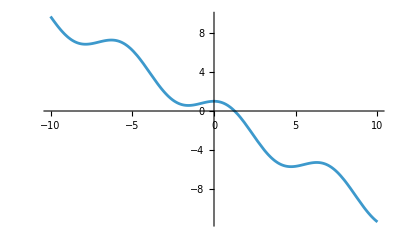

```mathematica
Plot[Sin[x]+Cos[x]-x,{x,-10,10}]
```

```mathematica
FindRoot[Sin[x]+Cos[x]==x,{x,1}]
```

{x→1.25873}

```mathematica
RSolve[{a[n+1]==1/3*a[n]+1,a[0]==0},a[n],n]
```

{{a[n]→1/2 3^(1-n) (-1+3^n)}}

```mathematica
a=6378
b=6358
N[Integrate[Sqrt[a^2*Sin[t]^2+b^2*Cos[t]^2],{t, 0, 2*Pi}]]
```

40011.3

```mathematica
N[2*Pi*a]
```

40074.2

```mathematica
-
```

62.8072

```mathematica
Expand[Sum[x^(5*k), {k, 0, 20}]*Sum[x^(10*l), {l, 0, 10}]*Sum[x^{20*m}, {m, 0, 5}]]
```

{1+x^5+2 x^10+2 x^15+4 x^20+4 x^25+6 x^30+6 x^35+9 x^40+9 x^45+12 x^50+12 x^55+16 x^60+16 x^65+20 x^70+20 x^75+25 x^80+25 x^85+30 x^90+30 x^95+36 x^100+35 x^105+40 x^110+39 x^115+44 x^120+42 x^125+46 x^130+44 x^135+48 x^140+45 x^145+48 x^150+45 x^155+48 x^160+44 x^165+46 x^170+42 x^175+44 x^180+39 x^185+40 x^190+35 x^195+36 x^200+30 x^205+30 x^210+25 x^215+25 x^220+20 x^225+20 x^230+16 x^235+16 x^240+12 x^245+12 x^250+9 x^255+9 x^260+6 x^265+6 x^270+4 x^275+4 x^280+2 x^285+2 x^290+x^295+x^300}

```mathematica
Coefficient[Sum[x^(5*k), {k, 0, 200}]*Sum[x^(10*l), {l, 0, 100}]*Sum[x^{20*m}, {m, 0, 50}],x,1000]
```

{2601}

```mathematica
PolynomialRemainder[3x^2+15x+18,x^2+3x+2,x]
```

12+6 x

```mathematica
Clear[a,b]
Reduce[{a+b+c==11990, a^2+b^2==c^2}, {a,b,c}, PositiveIntegers]
```

(a==109&&b==5940&&c==5941)||(a==5940&&b==109&&c==5941)

```mathematica
PrimeQ[109]
```

True

```mathematica
Solve[x^4+x^3-3x^2-x+1==0,x,Quartics->True]
```

{{x→1/4 (-1+√5-√(2 (11-√5)))},{x→1/4 (-1+√5+√(2 (11-√5)))},{x→1/4 (-1-√5-√(2 (11+√5)))},{x→1/4 (-1-√5+√(2 (11+√5)))}}